```mathematica
$HistoryLength=0;
```

#### Levy vs const. external input

```mathematica
spikes=GroupBy[#,First->Last]&@ReadList["/import/headnode1/wardak/Desktop/superdiffapprox/data13_constantinput1/alpha1.20espikes-54001-"<>IntegerString[#,10,2]<>".gdf",Number,RecordLists->True]&~ParallelMap~Range[0,31]//Merge[Flatten]//Values;
```

```mathematica
ispikes=GroupBy[#,First->Last]&@ReadList["/import/headnode1/wardak/Desktop/superdiffapprox/data13_constantinput1/alpha1.20ispikes-54002-"<>IntegerString[#,10,2]<>".gdf",Number,RecordLists->True]&~ParallelMap~Range[0,31]//Merge[Flatten]//Values;
```

```mathematica
{Length@#,ByteCount[#]/2.^20}&/@{spikes,ispikes}
```

{{39999,582.095},{10000,144.278}}

```mathematica
With[{k=k/.Simplify[First@Solve[Mean[ParetoDistribution[k,α]]==J,{k}],Assumptions->α==1.2&&J==0.02]},Fold[#1+RandomVariate[ParetoDistribution[k,1.2]]*MapAt[1&,ConstantArray[0,100001],List/@#2]&,ConstantArray[0,100001],10spikes+1]]//BinarySerialize
```

ByteArray[…]

```mathematica
eLFP=BinaryDeserialize@NotebookRead[PreviousCell[]][[1,1,2]];
```

```mathematica
eLFPs=ParallelTable[With[{k=k/.Simplify[First@Solve[Mean[ParetoDistribution[k,α]]==J,{k}],Assumptions->α==1.2&&J==0.02]},Fold[#1+RandomVariate[ParetoDistribution[k,1.2]]*MapAt[1&,ConstantArray[0,100001],List/@#2]&,ConstantArray[0,100001],10RandomSample[spikes,4000]+1]],100];
```

```mathematica
With[{k=k/.Simplify[First@Solve[Mean[ParetoDistribution[k,α]]==J,{k}],Assumptions->α==1.2&&J==0.08]},Fold[#1+RandomVariate[ParetoDistribution[k,1.2]]*MapAt[1&,ConstantArray[0,100001],List/@#2]&,ConstantArray[0,100001],10ispikes+1]]//BinarySerialize
```

ByteArray[…]

```mathematica
iLFP=BinaryDeserialize@NotebookRead[PreviousCell[]][[1,1,2]];
```

```mathematica
iLFPs=ParallelTable[With[{k=k/.Simplify[First@Solve[Mean[ParetoDistribution[k,α]]==J,{k}],Assumptions->α==1.2&&J==0.08]},Fold[#1+RandomVariate[ParetoDistribution[k,1.2]]*MapAt[1&,ConstantArray[0,100001],List/@#2]&,ConstantArray[0,100001],10RandomSample[ispikes,1000]+1]],100];
```

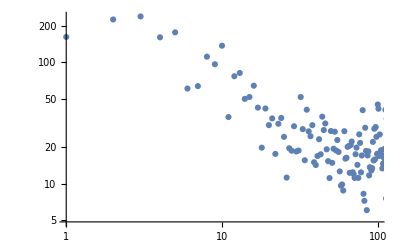

```mathematica
Periodogram[#[[60002;;]]&/@(eLFPs+iLFPs)//Flatten,10000,SampleRate->10000,ScalingFunctions->{"Log","Log"},PlotRange->{{10^0,10^2},Automatic},PlotMarkers->{Automatic}]/.Line->Point
```

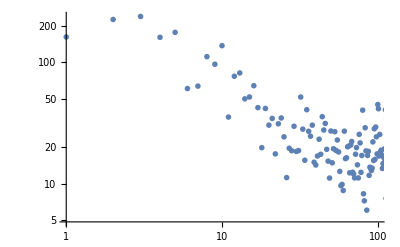

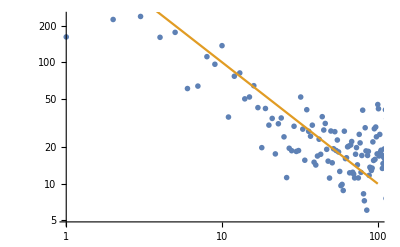

```mathematica
Periodogram[#[[60002;;]]&/@(eLFPs+iLFPs)//Flatten,10000,SampleRate->10000,ScalingFunctions->{"Log","Log"},PlotRange->{{10^0,10^2},Automatic},PlotMarkers->"OpenMarkers"]/.Line->Point
```

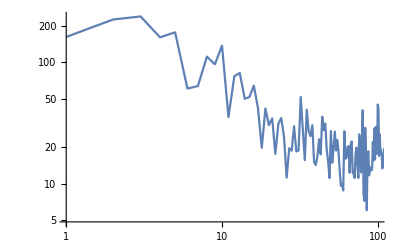

```mathematica
Periodogram[#[[60002;;]]&/@(eLFPs+iLFPs)//Flatten,10000,SampleRate->10000,PlotRange->{{10^0,10^2},Automatic},ScalingFunctions->{"Log","Log"}]
```

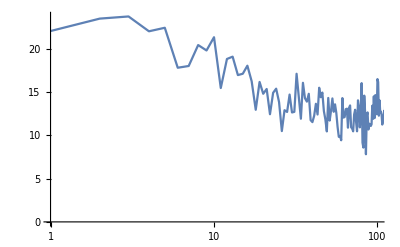

```mathematica
PeriodogramArray[#[[60002;;]]&/@(eLFPs+iLFPs)//Flatten,10000]//10Log10[#]&//ListLinePlot[#,DataRange->{0,10000},PlotRange->{{10^0,10^2},Automatic},ScalingFunctions->{"Log",Automatic}]&
```

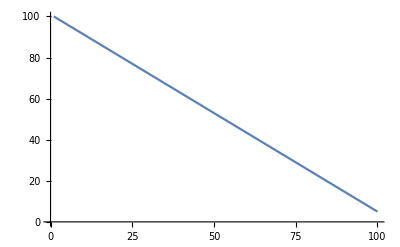

```mathematica
ListLinePlot[{{1,100},{100,5}}]
```

```mathematica
Show[-Graphics-,ListLinePlot[{{1,100},{100,5}}]]
```

-Graphics-

```mathematica
Periodogram[#[[60002;;]]&/@(eLFPs+iLFPs)//Flatten,10000,SampleRate->10000,ScalingFunctions->"Absolute"]//Cases[#,Line[data_]:>data,∞]&//BinarySerialize
```

ByteArray[…]

```mathematica
BinaryDeserialize[NotebookRead[PreviousCell[]][[1,1,2]]]
```

{{{5.56399,111.176},{6.0012,60.7306},{7.0014,63.6209},{8.0016,111.126},{9.0018,96.2175},{9.36972,111.176}},{1},18,{1},{{4741.02,111.176},{4741.95,23.4882},{4742.95,53.2306},{4743.95,42.2644},253,{4998.,37.0893},{4999.,43.0821},{5000.,54.4681}}}
 |  |  |  |

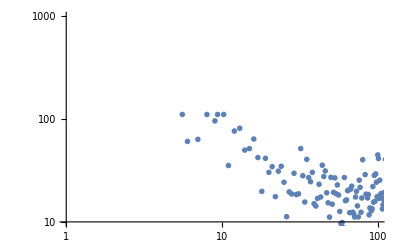

```mathematica
BinaryDeserialize[NotebookRead[PreviousCell[]][[1,1,2]]]//Apply[Join]//ListPlot[#,ScalingFunctions->{"Log","Log"},PlotRange->{{10^0,10^2},{10^1,10^3}},PlotMarkers->"OpenMarkers"]&
```

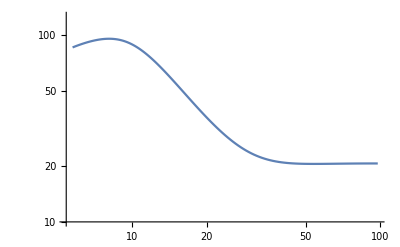

```mathematica
BinaryDeserialize[NotebookRead[PreviousCell[]][[1,1,2]]]//Apply[Join]//TakeList[#,NestList[2#&,2,5]]&//Map[First@MovingAverage[#,Length@#]&]//ListLinePlot[#,ScalingFunctions->{"Log","Log"},InterpolationOrder->5,PlotRange->{10^1,10^2.1}]&
```

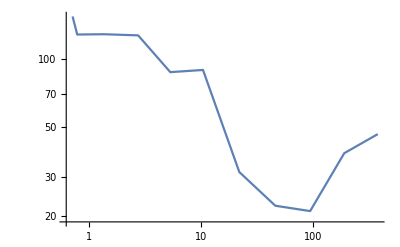

```mathematica
Periodogram[#[[60002;;]]&/@(eLFPs+iLFPs)//Flatten,40000,SampleRate->10000,ScalingFunctions->"Absolute"]//Cases[#,Line[data_]:>data,∞]&//Apply[Join]//TakeList[#,NestList[2#&,1,10]]&//Map[First@MovingAverage[#,Length@#]&]//ListLinePlot[#,ScalingFunctions->{"Log","Log"}]&
```

```mathematica
Periodogram[#[[60002;;]]&/@(eLFPs+iLFPs)//Flatten,10000,SampleRate->10000]//BinarySerialize
```

ByteArray[…]

```mathematica
MovingAverage[{{1,2},{3,44}},2]
```

{{2,23}}

```mathematica
ListLinePlot[#,ScalingFunctions->{"Log","Log"},PlotRange->{{10^0,10^2},Automatic},InterpolationOrder->None]
```

```mathematica
NotebookSave[]
```

```mathematica
Table[GroupBy[#,First@*Rest->Last,First]&@Select[EqualTo[i]@*First]@ReadList["/import/headnode1/wardak/Desktop/superdiffapprox/data13_constantinput3/alpha1.20V_m-54003-"<>IntegerString[#,10,2]<>".dat",Number,RecordLists->True]&~ParallelMap~Range[0,31]//Merge[Flatten]//Values//Flatten,{i,RandomSample[Range[40000],5]}]//BinarySerialize
```

ByteArray[…]

```mathematica
Vtimes=BinaryDeserialize@NotebookRead[PreviousCell[]][[1,1,2]];
```

```mathematica
test=GroupBy[#,First->Rest,GroupBy[#,First->Last,First]&]&@Select[LessThan[10000]@*First]@ReadList["/import/headnode1/wardak/Desktop/superdiffapprox/data13_constantinput3/alpha1.20V_m-54003-"<>IntegerString[#,10,2]<>".dat",Number,RecordLists->True]&~ParallelMap~Range[0,31]//Merge[Values@*KeySort@*Merge[First]];
```

```mathematica
test=GroupBy[#,First->Rest,GroupBy[#,First->Last,First]&]&@Select[LessThan[10000]@*First]@ReadList["/import/headnode1/wardak/Desktop/superdiffapprox/data13_constantinput3/alpha1.20V_m-54003-"<>IntegerString[#,10,2]<>".dat",Number,RecordLists->True]&~ParallelMap~Range[0,31]//Merge[Values@*Merge[First]];
```

```mathematica
ByteCount[test]/2^20//N
```

765.582

```mathematica
Flatten/@Transpose[#~Partition~4999&/@Values@test]//Dimensions
```

{2,4994001}

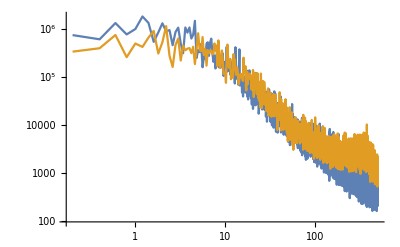

```mathematica
Periodogram[Flatten/@Transpose[#~Partition~4999&/@Values@test],4999,SampleRate->1000,ScalingFunctions->{"Log","Log"}]
```

```mathematica
Dimensions@Values@test
```

{9999,9999}

```mathematica
Table[Show[Periodogram[#~Partition~4999,1000,SampleRate->1000,ScalingFunctions->{"Log","Log"},PlotRange->Full,PlotStyle->Opacity[.5]]&/@Values@RandomSample[test,10],PlotRange->{Log@{1,100},Full}],100]~Partition~10//Grid
```

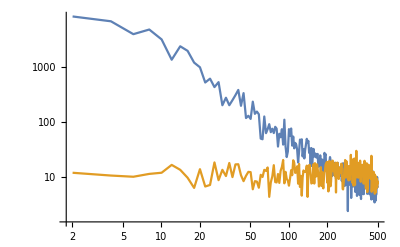

```mathematica
Periodogram[Flatten@Values@Vtime~Partition~4999,500,SampleRate->1000,ScalingFunctions->{"Log","Log"},PlotRange->All]
```

```mathematica
(*1: wrong units; 2: same amplitude as noisy ext input; 3: 2x amplitude; 4: 5x amplitude*)
```

```mathematica
V=ReadList["/import/headnode1/wardak/Desktop/superdiffapprox/data13_constantinput10/alpha1.20V_m-54003-01.dat",Number,RecordLists->True];
```

```mathematica
Vs=GatherBy[V,#[[2]]>5000&];
```

```mathematica
Skewness[Select[#[[All,3]],GreaterThan[10]]]&/@Vs
```

{0.429506,0.179211}

```mathematica
Table[Transpose[{MovingAverage[#1,2],#2/(Length@v*First@Differences@Subdivide[5,25,120-1])}]&@@HistogramList[Select[v[[All,3]],#≠10&],List@Subdivide[5,25,120-1]]//BinarySerialize,{v,Vs}]
```

{ByteArray[…],ByteArray[…]}

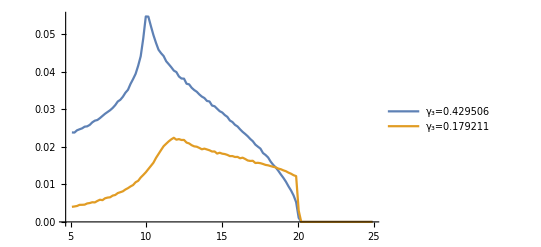

```mathematica
ListLinePlot[BinaryDeserialize/@{ByteArray[…],ByteArray[…]},PlotLegends->(HoldForm[Subscript[γ, 3]=#]&/@{0.42950636151244126,0.17921149248284252})~Placed~{0.8,0.8}]
```

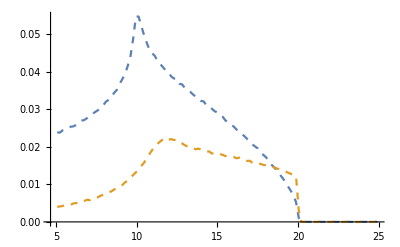

```mathematica
ListLinePlot[BinaryDeserialize/@{ByteArray[…],ByteArray[…]},PlotStyle->Dashed]
```

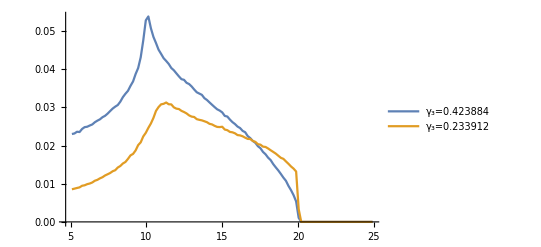

```mathematica
ListLinePlot[BinaryDeserialize/@{ByteArray[…],ByteArray[…]},PlotLegends->(HoldForm[Subscript[γ, 3]=#]&/@{0.42388364504906156,0.2339124822671306})~Placed~{0.8,0.8}]
```

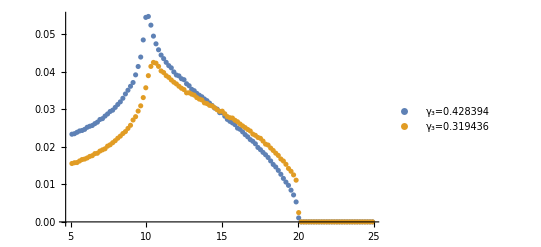

```mathematica
ListPlot[BinaryDeserialize/@{ByteArray[…],ByteArray[…]},PlotLegends->(HoldForm[Subscript[γ, 3]=#]&/@{0.42839377845083204,0.31943648201808433})~Placed~{0.8,0.8}]
```

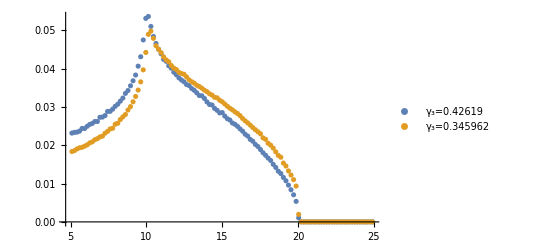

```mathematica
ListPlot[BinaryDeserialize/@{ByteArray[…],ByteArray[…]},PlotLegends->(HoldForm[Subscript[γ, 3]=#]&/@{0.4261896563606164,0.3459617170520391})~Placed~{0.8,0.8}]
```

#### Network firing rate over alphas

```mathematica
spikesalphas=Table[Merge[CountsBy[First]@ReadList["/import/headnode1/wardak/Desktop/superdiffapprox/data13/alpha"<>alpha<>"espikes-54001-"<>IntegerString[#,10,2]<>".gdf",Number,RecordLists->True]&~ParallelMap~Range[0,31],Total],{alpha,{"1.05","1.10","1.20","1.40","1.60","1.80"}}]~Join~List@Merge[CountsBy[First]@ReadList["/import/headnode1/wardak/Desktop/superdiffapprox/data13/alpha2.00espikes-50002-"<>IntegerString[#,10,2]<>".gdf",Number,RecordLists->True]&~ParallelMap~Range[0,31],Total];
```

```mathematica
27871*10/40000//N
```

6.96775

```mathematica
Length@*Keys/@spikesalphas
```

{27871,39973,39999,40000,40000,40000,40000}

```mathematica
Through@{Mean,StandardDeviation,Quantile[#,{0.05,0.95}]&}[Values[#]]&/@spikesalphas/100.//Transpose
```

{{6.9577,65.9472,47.0917,29.0975,22.7995,20.0547,18.1513},{8.70948,58.4781,33.5594,11.5816,5.08076,2.34144,0.0924461},{{0.02,24.27},{2.72,185.97},{5.47,112.25},{12.,49.51},{15.26,31.82},{16.75,24.23},{18.,18.3}}}

```mathematica
Apply@Moment/@Transpose[Values[spikesalphas/100.]~List~{1.05,1.1,1.2,1.4,1.6,1.8,2.0}]
```

{7.94933,104.375,107.718,116.972,152.342,222.951,329.477}

```mathematica
With[{g=4,γ=0.25,α=1.2},Through@{Mean,StandardDeviation,Moment[Abs[#-g γ^(1/α)RandomSample[#]],α]&,With[{ν=#-g γ^(1/α)RandomSample[#]},Moment[Sign[ν]Abs[ν]^α,1]/Moment[Abs[ν],α]]&}[Values[spikesalphas[[3]]/100.]]]
```

{47.0917,33.5594,96.5186,-0.312216}

#### Network firing rate distribution alpha=1.2

```mathematica
(*@Select[GreaterThan[1000]@*Last] makes no difference, along with inhibitory populations*)
```

```mathematica
spikes=Merge[CountsBy[First]@ReadList["/import/headnode1/wardak/Desktop/superdiffapprox/data13/alpha1.20espikes-54001-"<>IntegerString[#,10,2]<>".gdf",Number,RecordLists->True]&~ParallelMap~Range[0,31],Total];
```

```mathematica
BinarySerialize@Values[spikes/100]
```

ByteArray[…]

```mathematica
firingrate=BinaryDeserialize@NotebookRead[PreviousCell[]][[1,1,2]];
```

```mathematica
With[{g=4,γ=0.25,α=1.2},Through@{Mean,StandardDeviation,Moment[Abs[#-g γ^(1/α)RandomSample[#]],α]&,With[{ν=#-g γ^(1/α)RandomSample[#]},Moment[Sign[ν]Abs[ν]^α,1]/Moment[Abs[ν],α]]&}[firingrate]]//N
```

{47.0917,33.5594,97.1576,-0.311627}

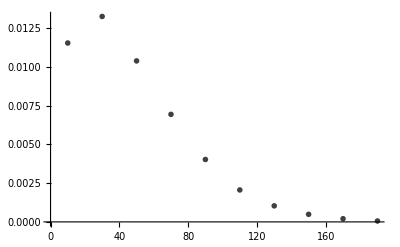

```mathematica
With[{nbins=10},ListPlot[Transpose[{MovingAverage[#1,2],#2/(Length@firingrate*First@Differences@Subdivide[0,200,(nbins+1)-1])}],PlotMarkers->{"Δ",16},PlotStyle->Opacity[0.75,Black]]&@@HistogramList[firingrate,List@Subdivide[0,200,(nbins+1)-1]]]
```

```mathematica
Show[With[{mean=80,sd=80},With[{μ=Log[mean^2/Sqrt[sd^2+mean^2]],σ=Log[sd^2/mean^2+1]},Plot[Exp[-(Log@x-μ)^2/(2σ^2)]/(x σ Sqrt[2π]),{x,10,500},ScalingFunctions->{"Log"},PlotStyle->Gray]]],ListPlot[Transpose[{MovingAverage[#1,2],#2}]&@@HistogramList[firingrate,{"Log",30},"PDF"],ScalingFunctions->{"Log"},PlotRange->{{10,500},Automatic},PlotMarkers->"Δ",PlotStyle->Opacity[0.5,Black]]]
```

-Graphics-

#### Network mean V per neuron distribution (Tan, fig. 2(e))

```mathematica
V=GroupBy[First->Last]@ReadList["/import/headnode1/wardak/Desktop/superdiffapprox/data9/alpha1.20V_m-54003-"<>IntegerString[#,10,2]<>".dat",Number,RecordLists->True]&~ParallelMap~Range[0,31]//Merge[Flatten];
```

```mathematica
ByteCount[V]/2^30.
```

11.1855

```mathematica
BinarySerialize@Values[Skewness@*Select[GreaterThan@10]/@V]
```

Skewness::shlen: The argument {} should have at least two elements.

Skewness::shlen: The argument {12.408} should have at least two elements.

Skewness::shlen: The argument {} should have at least two elements.

General::stop: Further output of Skewness::shlen will be suppressed during this calculation.

ByteArray[…]

```mathematica
skewnessV=BinaryDeserialize@NotebookRead[PreviousCell[]][[1,1,2]];
```

Skewness::shlen: The argument {} should have at least two elements.

Skewness::shlen: The argument {12.408} should have at least two elements.

Skewness::shlen: The argument {} should have at least two elements.

General::stop: Further output of Skewness::shlen will be suppressed during this calculation.

```mathematica
BinarySerialize@Values[Skewness/@V]
```

ByteArray[…]

```mathematica
skewnessV2=BinaryDeserialize@NotebookRead[PreviousCell[]][[1,1,2]];
```

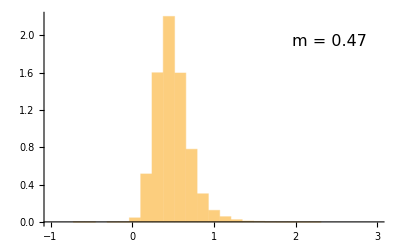

```mathematica
Histogram[Select[NumberQ]@skewnessV,List@Subdivide[-1,3,30-1],"PDF",Epilog->Text[Style["m = "<>ToString@(NumberForm[Median@Select[NumberQ]@skewnessV,2]),16],Scaled@{.95,.9},{Right,Top}]]
```

```mathematica
BinarySerialize@Values[Mean/@V]
```

ByteArray[…]

```mathematica
meanV=BinaryDeserialize@NotebookRead[PreviousCell[]][[1,1,2]];
```

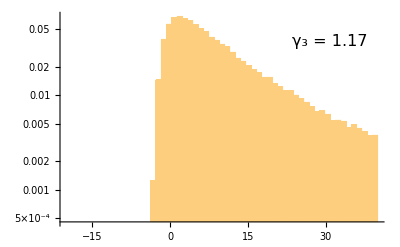

```mathematica
Histogram[(*Mean[#]*)10-#&@meanV,List@Subdivide[-20,40,60-1],"PDF",ScalingFunctions->"Log",Epilog->Text[Style["γ_3 = "<>ToString@(NumberForm[Skewness[(*Mean[#]*)10-#],3]&@Select[GreaterThan[-30]]@meanV),16],Scaled@{.95,.9},{Right,Top}]]
```

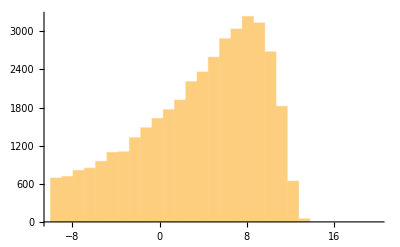

```mathematica
Histogram[meanV,List@Subdivide[-10,20,30-1]]
```